```mathematica
SetDirectory["/Users/mobileryan/Triplet-ESR"]
```

/Users/mobileryan/Triplet-ESR

```mathematica
Directory[]
```

C:\Users\goluc\Documents

```mathematica
SetDirectory["C:\\Users\\goluc\\Desktop\\nonLinearFit"]
```

C:\Users\goluc\Desktop\nonLinearFit

```mathematica
preData=Import["./test.dat","CSV" ];
{dimT, dump}=Dimensions[preData[[2;;-1]]]
BData=Drop[Drop[preData[[1]],1],-1];
dimB=Length[BData]
DataB[B_]:=Table[{preData[[i,1]],preData[[i,B+1]]},{i,2,dimT}]
DataT[t_]:=Table[{preData[[1,i]],preData[[t+1,i+1]]},{i,1,dimB}]
```

{1002,352}

350

```mathematica
tempData=preData[[2;;-1, 2;;-1]];
ArrayPlot[tempData,ColorFunction->"Rainbow",AspectRatio->1]
{Max[tempData], Min[tempData]}
```

-Graphics-

{Max[41.34,],Min[-34.17,]}

```mathematica
Manipulate[
Module[{dataT},
dataT=DataT[startT];
ListPlot[dataT,Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full, PlotLabel->ToString[startT]<>", Time = "<>ToString[preData[[startT+1,1]]]<>", Max = "<> ToString[Max[dataT[[1;;-1,2]]]]<>", Min = "<>ToString[ Min[dataT[[1;;-1,2]]]]] 
],
{{startT,207},1,dimT,1}]
```

```mathematica
Manipulate[
Module[{dataB},
dataB=DataB[startB];
ListPlot[dataB,Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full, PlotLabel->ToString[startB]<>", B-field = "<>ToString[preData[[1,startB]]]<>", Max = "<> ToString[Max[dataB[[1;;-1,2]]]]<>", Min = "<>ToString[ Min[dataB[[1;;-1,2]]]]]
] ,
{{startB,105},1,dimB,1}]
```

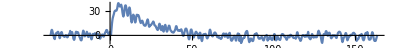

{B-Field,3.361,2.8,mean,0.685424,sd,2.94256}

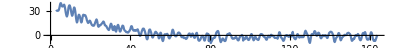

```mathematica
startB=141;
dataB=DataB[startB];
fitStartT=197;
ListPlot[dataB, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full] 
{"B-Field",BData[[startB]],dataB[[fitStartT,1]],"mean",noiseLevel=Mean[dataB[[1;;fitStartT-20,2]]], "sd",sd=StandardDeviation[dataB[[1;;fitStartT-20,2]]]}
g1=ListPlot[dataB[[fitStartT;;-1]], Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
```

```mathematica
Func[t_,a_,Ta_]:=a Exp[-t/Ta]
f[t_,par_]:=Func[t,par[[1]],par[[2]]]+Func[t,par[[3]],par[[4]]]
F[t_,par_]:={ⅇ^(-t/par[[2]]),(par[[1]] ⅇ^(-t/par[[2]]) t)/par[[2]]^2,ⅇ^(-t/par[[4]]),(par[[3]] ⅇ^(-t/par[[4]]) t)/par[[4]]^2}
F2[t_,par_]:={ⅇ^(-t/par[[2]]),(par[[1]] ⅇ^(-t/par[[2]]) t)/par[[2]]^2}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 100. | 203.999 | 0.490199 | 0.62413
Ta | 32.6862 | 13.0036 | 2.51362 | 0.0121497
b | -56.5104 | 204.612 | -0.276183 | 0.782481
Tb | 46.7132 | 28.7862 | 1.62276 | 0.105043, | DF | SS | MS
Model | 4 | 80441.2 | 20110.3
Error | 782 | 8368.16 | 10.701
Uncorrected Total | 786 | 88809.3 | 
Corrected Total | 785 | 77777.3 | , | Estimate | Standard Error | Confidence Interval
a | 100. | 203.999 | {-300.45,500.45}
Ta | 32.6862 | 13.0036 | {7.16006,58.2123}
b | -56.5104 | 204.612 | {-458.165,345.144}
Tb | 46.7132 | 28.7862 | {-9.79421,103.221}}

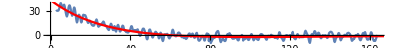

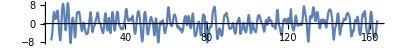

{mean,0.0615063,sd,3.24995,1.10446}

```mathematica
nlm=NonlinearModelFit[dataB[[fitStartT;;-20]],{f[t,{a,Ta,b,Tb}], 100>a>0, b<0, 0<Ta <Tb}, {a, Ta, b, Tb}, t];
nlm[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
Show[
g1,
Plot[nlm[t],{t,0,200}, PlotRange->All, PlotStyle->Red]
]
diff=Table[{dataB[[i,1]],dataB[[i,2]]-nlm[dataB[[i,1]]]},{i,200,Length[dataB]}];
ListPlot[diff, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
{"mean",Mean[diff[[1;;-1,2]]], "sd",fitSigma=StandardDeviation[diff[[1;;-1,2]]], fitSigma/sd}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 43.2005 | 0.907993 | 47.5781 | 3.98102×10^-236
Ta | 18.0898 | 0.468966 | 38.5738 | 3.69199×10^-185, | DF | SS | MS
Model | 2 | 64018.5 | 32009.3
Error | 805 | 8658.36 | 10.7557
Uncorrected Total | 807 | 72676.9 | 
Corrected Total | 806 | 64550.3 | , | Estimate | Standard Error | Confidence Interval
a | 43.2005 | 0.907993 | {41.4182,44.9828}
Ta | 18.0898 | 0.468966 | {17.1693,19.0104}}

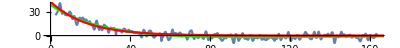

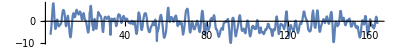

{mean,-1.00226,sd,3.05819,1.04221}

```mathematica
nlm2=NonlinearModelFit[dataB[[fitStartT;;-1]],{Func[t,a,Ta], 100>a>0, 0<Ta}, {a, Ta}, t];
nlm2[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
Show[
g1,
Plot[nlm[t],{t,0,200}, PlotRange->All, PlotStyle->Green],
Plot[nlm2[t],{t,0,200}, PlotRange->All, PlotStyle->Red]
]
diff2=Table[{dataB[[i,1]],dataB[[i,2]]-nlm2[dataB[[i,1]]]},{i,200,Length[dataB]}];
ListPlot[diff2, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
{"mean",Mean[diff2[[1;;-1,2]]], "sd",fitSigma2=StandardDeviation[diff2[[1;;-1,2]]], fitSigma2/sd}
```

## Manual Method

```mathematica
newPar[par_,dataB_]:=Module[
{fa,Fa, Y,X, par1,CoVar, error, var, DF, GMat},
X=dataB[[1;;-1,1]];
Y=dataB[[1;;-1,2]];
fa=Table[f[X[[i]], par],{i,Length[X]}];
Fa=Table[F[X[[i]], par],{i,Length[X]}];
GMat=Inverse[Transpose[Fa].Fa].Transpose[Fa];
par1=par+GMat.(Y-fa);
DF=Length[X]-Length[par];
var=(Y-fa).(Y-fa)/DF;
CoVar=var Inverse[Transpose[Fa].Fa];
Print[CoVar//MatrixForm];
error=Table[√CoVar[[i,i]],{i,1,Length[par]}];
{par1,error, var,DF}
]
```

```mathematica
temp=newPar[{60,35,-30,60},dataB[[fitStartT;;-1]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-1]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-1]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-1]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-1]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-1]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-1]]]
temp=newPar[temp[[1]],dataB[[fitStartT;;-1]]]
```

{{58.2725,28.2107,-19.3445,57.6142},{71.4835,12.6618,72.0725,37.4555},12.4731,803}

{{61.7463,29.7884,-22.6796,57.1035},{22.4085,4.81969,22.9219,22.9542},8.69103,803}

{{64.3452,30.2433,-25.3009,55.3887},{30.193,5.70507,30.7018,23.7913},8.62863,803}

{{64.3821,30.2293,-25.3363,55.5551},{37.3542,6.29141,37.8661,23.7052},8.62775,803}

{{64.4419,30.239,-25.3969,55.5162},{36.7558,6.22609,37.2673,23.505},8.62669,803}

{{64.436,30.2381,-25.3909,55.5202},{36.937,6.24026,37.4486,23.5065},8.62669,803}

{{64.4367,30.2382,-25.3916,55.5197},{36.9188,6.23883,37.4303,23.5063},8.62669,803}

{{64.4366,30.2382,-25.3915,55.5198},{36.9208,6.23899,37.4324,23.5063},8.62669,803}

```mathematica
nlm[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 64.4366 | 36.9206 | 1.74527 | 0.0813196
Ta | 30.2382 | 6.23898 | 4.84666 | 1.50726×10^-6
b | -25.3915 | 37.4322 | -0.678335 | 0.497755
Tb | 55.5197 | 23.5063 | 2.36191 | 0.018419, | DF | SS | MS
Model | 4 | 65749.6 | 16437.4
Error | 803 | 6927.23 | 8.62669
Uncorrected Total | 807 | 72676.9 | 
Corrected Total | 806 | 64550.3 | , | Estimate | Standard Error | Confidence Interval
a | 64.4366 | 36.9206 | {-8.03572,136.909}
Ta | 30.2382 | 6.23898 | {17.9916,42.4848}
b | -25.3915 | 37.4322 | {-98.868,48.0849}
Tb | 55.5197 | 23.5063 | {9.37862,101.661}}

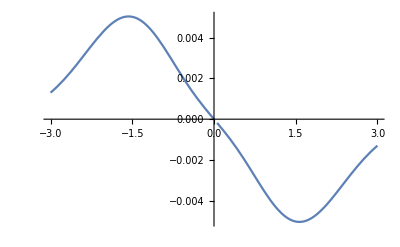

```mathematica
Plot[{
CDF[StudentTDistribution[30],x]-CDF[StudentTDistribution[800],x]
},{x,-3,3}]
```

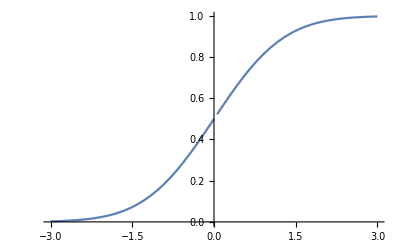

```mathematica
Plot[{
CDF[StudentTDistribution[30],x]
},{x,-3,3}]
```

```mathematica
tDis30=Table[{x,CDF[StudentTDistribution[30],x]},{x,-3,3,0.01}];
```

```mathematica
Manipulate[Show[
ListPlot[Evaluate[Table[{x,CDF[StudentTDistribution[DF],x]},{x,-3,3,0.01}]], Joined->True],
Plot[1/(1+Exp[-x/a]),{x,-3,3}, PlotStyle-> Red]
],
{DF,2,10,1},
{a,0.6,1}]
```

```mathematica
app=NonlinearModelFit[tDis30,{1/(1+Exp[-x/a]), 100>a>0}, {a}, x];
app["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.600984 | 0.000925527 | 649.343 | 1.94413513272×10^-856

```mathematica
DF=803;α=0.95;
tStat=Table[temp[[1,i]]/temp[[2,i]],{i,1,4}]
pValue=Table[2(1-CDF[StudentTDistribution[DF],Abs[tStat[[i]]]]),{i,1,4}]
CF=Table[
temp[[1,i]]+
temp[[2,i]]{InverseCDF[StudentTDistribution[DF],(1-α)/2],InverseCDF[StudentTDistribution[DF],(1+α)/2]},{i,1,4}]
```

{1.74526,4.84665,-0.678331,2.36191}

{0.0813214,1.50736×10^-6,0.497757,0.018419}

{{-8.03612,136.909},{17.9915,42.4848},{-98.8684,48.0853},{9.37862,101.661}}

```mathematica
newPar2[par_,dataB_]:=Module[
{fa,Fa, Y,X, par1,CoVar, error, var, DF, GMat},
X=dataB[[1;;-1,1]];
Y=dataB[[1;;-1,2]];
fa=Table[Func[X[[i]], par[[1]],par[[2]]],{i,Length[X]}];
Fa=Table[F2[X[[i]], par],{i,Length[X]}];
GMat=Inverse[Transpose[Fa].Fa].Transpose[Fa];
par1=par+GMat.(Y-fa);
DF=Length[X]-Length[par];
var=(Y-fa).(Y-fa)/DF;
CoVar=var Inverse[Transpose[Fa].Fa];
error=Table[√CoVar[[i,i]],{i,1,Length[par]}];
{par1,error, var,DF}
]
```

```mathematica
temp2=newPar2[{50,30},dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
```

{{42.0385,18.115},{1.32321,1.03401},47.0199,805}

{{43.21,18.0827},{0.909289,0.483381},10.8097,805}

{{43.1979,18.0916},{0.908267,0.468798},10.7557,805}

{{43.2012,18.0894},{0.907925,0.469012},10.7557,805}

{{43.2004,18.0899},{0.908009,0.468955},10.7557,805}

{{43.2006,18.0898},{0.907988,0.468969},10.7557,805}

{{43.2005,18.0898},{0.907994,0.468966},10.7557,805}

{{43.2005,18.0898},{0.907992,0.468966},10.7557,805}

```mathematica
nlm2[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 43.2005 | 0.907993 | 47.5781 | 3.98102×10^-236
Ta | 18.0898 | 0.468966 | 38.5738 | 3.69199×10^-185, | DF | SS | MS
Model | 2 | 64018.5 | 32009.3
Error | 805 | 8658.36 | 10.7557
Uncorrected Total | 807 | 72676.9 | 
Corrected Total | 806 | 64550.3 | , | Estimate | Standard Error | Confidence Interval
a | 43.2005 | 0.907993 | {41.4182,44.9828}
Ta | 18.0898 | 0.468966 | {17.1693,19.0104}}

```mathematica
DF2=805;α=0.95;
tStat2=Table[temp2[[1,i]]/temp2[[2,i]],{i,1,2}]
pValue2=Table[2(1-CDF[StudentTDistribution[DF2],Abs[tStat2[[i]]]]),{i,1,2}]
CF2=Table[
temp2[[1,i]]+
temp2[[2,i]]{InverseCDF[StudentTDistribution[DF2],(1-α)/2],InverseCDF[StudentTDistribution[DF2],(1+α)/2]},{i,1,2}]
```

{47.5777,38.5742}

{0.,0.}

{{41.4182,44.9828},{17.1693,19.0104}}